nrmma > GridFunctions

# GridFunctions

The GridFunctions Mathematica package provides a simple interface to grid data from numerical simulations.  It is currently capable of reading HDF5 and ASCII files produced by Carpet and returns variables as DataRegion objects.

## Common Arguments

Most of the functions in this package take at least two arguments: run and var and dims.

run: The name of the run directory containing the simulation files.

var: The name of the grid variable to be read.

dims: The dimensions to be read. These can be given either as a list of numbers of coordinate names ({1,2,3} or {“x”,”y”,”z”}) or asa combined string “xyz”.

The following options can be given:

Option			Default			Description
Iteration		0			The iteration to read.
Map			None			The map to read (use None for single map data, or an integer for multi-map)
RefinementLevel	0			The refinement level to read.
TimeLevel		0			The time level to read.
Variable		First in file		The variable to read

## Functions

Functions provided by GridFunctions.

### ReadGridFunction[run, var, dims]

Read a grid function for the variable var of dimension dims in run and return it as a DataRegion.

This function reads a variable from a simulation and returns it as a single DataRegion object. 
1D, 2D and 3D variables are currently supported.  If the file is part of a multi-file set, all the files will be used to read the variable.

If there is more than one component, the components will all be read and joined together into a single rectangular DataRegion.  If the union of the components is not rectangular, the smallest rectangular region surrounding all components will be used, and points not in any component will take the value None.

If the file appears in more than one segment, the correct segment for the given iteration will be located automatically.
In addition to the common options listed above, the following options can be given:

Option			Default			Description
StripGhostZones	True			Remove the ghost zones from the data

### ReadIterations[run, var, dims]

Read the iteration numbers present in run for var. If the options Map, RefinementLevel, TimeLevel or Variable are specified, then only iterations corresponding to those will be included.

### ReadMaps[run, var, dims]

Read the maps present in run for var. If the options Iteration, RefinementLevel, TimeLevel or Variable are specified, then only iterations corresponding to those will be included.

### ReadRefinementLevels[run, var, dims]

Read the refinement levels present in run for var. If the options Iteration, Map, TimeLevel or Variable are specified, then only iterations corresponding to those will be included.

### ReadTimeLevels[run, var, dims]

Read the timelevels present in run for var. If the options Iteration, Map, RefinementLevel or Variable are specified, then only iterations corresponding to those will be included.

### ReadTime[run, var, dims, it]

Read the coordinate time associated with this grid function at iteration it.

## Example

```mathematica
<<nrmma`
```

Examine the variable phi from the simulation bbh in the x-y plane.

```mathematica
ReadIterations["bbh","phi","xy"]//Short
```

{0,1024,2048,3072,4096,5120,6144,«5»,12288,13312,14336,15360,16384,17408,18432}

```mathematica
ReadRefinementLevels["bbh","phi","xy"]
```

{0,1,2,3,4,5,6}

```mathematica
ReadMaps["bbh","phi","xy"]
```

{}

```mathematica
ReadTime["bbh","phi","xy",Iteration->4096]
```

64.

```mathematica
ReadTimeLevels["bbh","phi","xy"]
```

{0}

```mathematica
phi=ReadGridFunction["bbh","phi","xy",Iteration->4096,RefinementLevel->3]
```

DataRegion[ML_BSSN::phi,<81,41>,{{0.,20.},{-10.,0.}}]

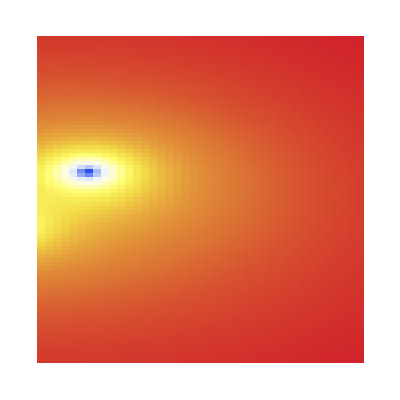
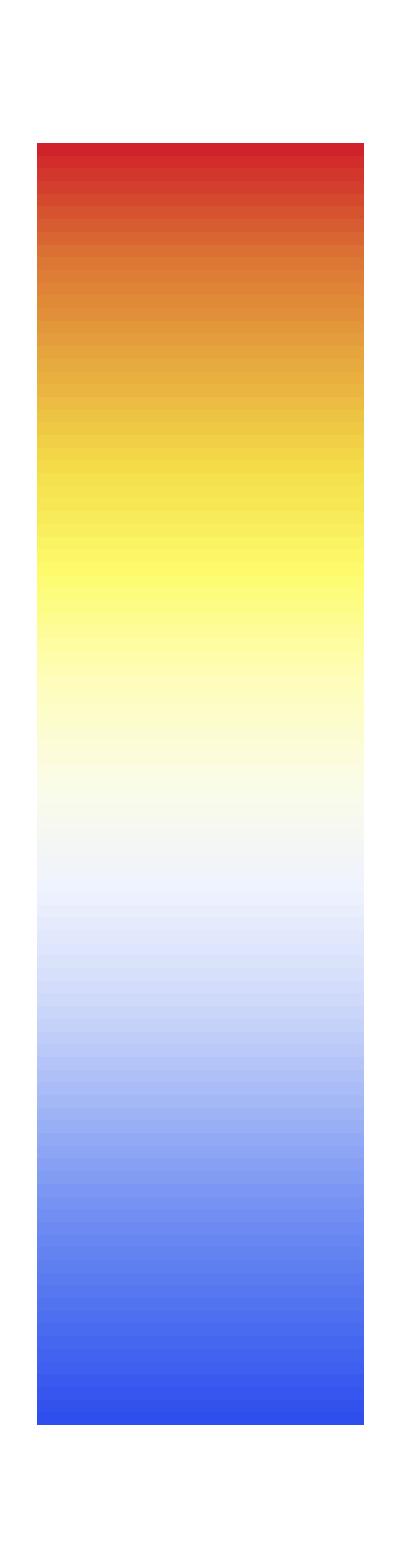

```mathematica
PresentationArrayPlot[phi]
```

RELATED TUTORIALS

DataRegion

NumericalRelativity